```mathematica
func[n_]:=Sqrt[2/l]Sin[n Pi x /l]
```

```mathematica
Integrate[func[1]v0 func[1],{x,3/8 l,5/8 l}]
```

((2 √2+π) v0)/(4 π)

```mathematica
Integrate[func[2]v0 func[2],{x,3/8 l,5/8 l}]
```

((-2+π) v0)/(4 π)

```mathematica
coef[k_]:=Integrate[func[1]v0 func[k],{x,3/8 l,5/8 l}]/(Pi^2hbar^2/(2 m l^2) (1-k^2))
```

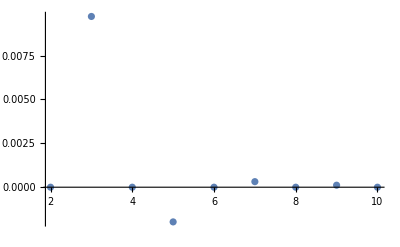

```mathematica
ListPlot[Table[{k,coef[k]/.{m->1,l->1,hbar->1,v0->1}},{k,2,10,1}],PlotRange->Full]
```

```mathematica
coef[k]
```

(2 l^2 m v0 (-(1+k) Sin[3/8 (-1+k) π]+(1+k) Sin[5/8 (-1+k) π]+(-1+k) (Sin[3/8 (1+k) π]-Sin[5/8 (1+k) π])))/(hbar^2 (-1+k) (1+k) (1-k^2) π^3)

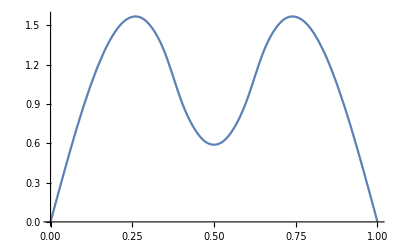

```mathematica
Plot[Evaluate[ func[1]+Sum[coef[k]func[k],{k,2,30}]/.{m->1,l->1,hbar->1,v0->50}],{x,0,1}]
```

```mathematica
func[1]Sum[coef[k]func[k],{k,2,10}]/.{m->1,l->1,hbar->1,v0->10}
```

√2 Sin[π x] ((5 (1+√2) Sin[3 π x])/(2 √2 π^3)-(5 (3+√2) Sin[5 π x])/(18 √2 π^3)+(5 Sin[7 π x])/(36 π^3)+Sin[9 π x]/(20 π^3))

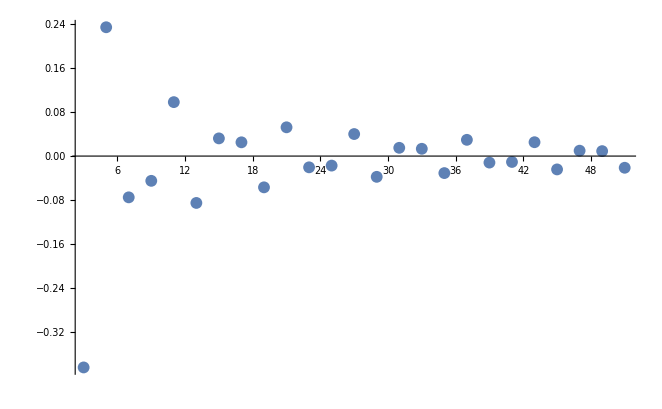

```mathematica
ListPlot[Table[{k,Integrate[func[1]v0 func[k],{x,3/8 l,5/8 l}]/.{m->1,l->1,hbar->1,v0->1}},{k,3,51,2}],PlotRange->Full]
```